### Scratch notes and plots for ps8 (e)

```mathematica
<<peeters` ;
peeters`setGitDir[ "figures/phy487" ]
```

peeters`

C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487

```mathematica
ContourPlot3D[ 1/Abs[ Sin[u] + Sin[v]] == e, {u, -Pi, Pi}, {v, -Pi, Pi}, {e, 0, 10}]
```

-Graphics3D-

```mathematica
Simplify[ Sin[ArcCos[a]]]
```

√(1-a^2)

```mathematica
$Assumptions = a > 0 ;
Clear[i]
i = Integrate[ E^(-2a Sqrt[x^2 + y^2 + z^2]) x^2, {x, -Infinity, Infinity}, {y, -Infinity, Infinity}, {z, -Infinity, Infinity}]
```

∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(-2 a √(x^2+y^2+z^2)) x^2ⅆzⅆyⅆx

```mathematica
i =  Integrate[ E^(-2a r) r^4 Sin[theta]^3 Cos[phi]^2, {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}]
```

π/a^5

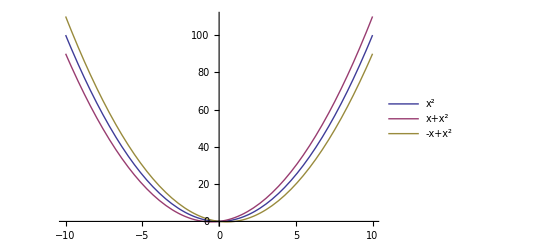

```mathematica
Plot[Evaluate@{x^2, x^2 + x, x^2 - x}, {x, -10, 10}, PlotLegends->"Expressions"]
```

```mathematica
Manipulate[
ContourPlot3D[ Cos[u] + Cos[v]== -mu  E^n, {u, -Pi, Pi}, {v, -Pi, Pi}, {mu, -2, 2}],
{n, 1/2, 5, 1/2}
]
```

```mathematica
Manipulate[
DynamicModule[{t, ticks},
t = Cos[u] + by Cos[v] == 2 #Sqrt[by^2 + 1] &/@ Table[n, {n, -1, 1, 0.1}] ;
ticks = Table[n, {n, -Pi, Pi, Pi/2}] ;
ContourPlot[ 
Evaluate@t
, {u, -Pi, Pi}
, {v, -Pi, Pi}
, FrameTicks -> {ticks, ticks}
, FrameLabel->{"k_x a", "k_y a"}
]
]
,{{by, 0.406}, 0, 1}
]
```

```mathematica
Clear[p]
p =DynamicModule[{by=0.406},DynamicModule[{t,ticks},t=(Cos[u]+by Cos[v]==2 #1 √(by^2+1)&)/@Table[n,{n,-1,1,0.1}];ticks=Table[n,{n,-π,π,π/2}];ContourPlot[Evaluate[t],{u,-π,π},{v,-π,π},FrameTicks->{ticks,ticks},FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\) a","\!\(\*SubscriptBox[\(k\), \(y\)]\) a"}]]]
```

```mathematica
peeters`exportForLatex["qmSolidsPs8eFig2", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs8eFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs8eFig2pn.png}

```mathematica
Manipulate[
DynamicModule[{t, ticks},
t = - Cos[u] + by Cos[v] == 2 #Sqrt[by^2 + 1] &/@ Table[n, {n, -1, 1, 0.1}] ;
ticks = Table[n, {n, -Pi, Pi, Pi/2}] ;
ContourPlot[ 
Evaluate@t
, {u, -Pi, Pi}
, {v, -Pi, Pi}
, FrameTicks -> {ticks, ticks}
, FrameLabel->{"k_x a", "k_y a"}
]
]
,{{by, 0.406}, 0, 1}
]
```

```mathematica
Clear[p]
p = DynamicModule[{by=0.406},DynamicModule[{t,ticks},t=(-Cos[u]+by Cos[v]==2 #1 √(by^2+1)&)/@Table[n,{n,-1,1,0.1}];ticks=Table[n,{n,-π,π,π/2}];ContourPlot[Evaluate[t],{u,-π,π},{v,-π,π},FrameTicks->{ticks,ticks},FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\) a","\!\(\*SubscriptBox[\(k\), \(y\)]\) a"}]]]

peeters`exportForLatex["qmSolidsPs8eFig2", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidsPs8eFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidsPs8eFig2pn.png}

```mathematica
(*peeters`exportForLatex["qmSolidsPs8eFig3", p]*)
(* http://mathematica.stackexchange.com/questions/1542/exporting-graphics-to-pdf-huge-file *)
(*Export["qmSolidsPs8eFig3f.pdf",p,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]*) (*1Mb*)

(* fork of exportForLatex ; looks about the same as the pdf export, but the final .eps -> .pdf is 40K instead of 1M *)
(*exportForLatexR[filename_, image_]  := Module[{output, dir},

dir = Directory[] ;
output =
{Export[filename  <> ".eps",First[ImportString[ExportString[image,"PDF","AllowRasterization"->True, Background->None],"PDF"]]]

,Export[filename  <> "pn.png", image ,"AllowRasterization"->True, Background->None, ImageResolution->72*4]
(*,Export[filename  <> ".pdf", image]*)
} ;
{dir <> "/" <> output[[1]], dir <> "/" <> output[[2]] }
]

exportForLatexR[ "qmSolidsPs8eFig3g",p]
*)
(* FIXME: try the "Before you fall into ... " solution next to get the antialiasing. *)

Clear[ p, by, size ]
by=0.406 ;
size = 800 ;

p = ContourPlot3D[ 
-Cos[u]+by Cos[v]==2 e √(by^2+1)
, {u, - Pi,  Pi}
, {v, - Pi,  Pi}
, {e, -1,  1}
(*, PlotLegends -> l (*Placed[ l , {Right,Top} ]*)*)
, Ticks -> {{-Pi, -Pi/2, 0, Pi/2, Pi}, {-Pi, -Pi/2, 0, Pi/2, Pi}, None}
,ImageSize->size
] 

antialias[g_]:=ImageResize[Rasterize[g,"Image",ImageResolution->72*2,Background->None],Scaled[1/2]]

img=antialias[Show[p,Axes->False,Boxed->False]] ;

Clear[plotopt]
plotopt::usage = "Extract the options for the plot p, retaining symbolic Tick values if set." ;
plotopt[p_] := Module[{t, ta},
t = Ticks /. Options[p] ;
ta = Ticks /. AbsoluteOptions[p] ;
AbsoluteOptions[p] /. ta -> t
]

Manipulate[
final=Graphics3D[Inset[img,ImageScaled[{s, t, u}],{Center,Center},sz],plotopt[p],ImageSize->sz]
,{{s, 0.505}, 0, 1}
,{{t, 0.414}, 0, 1}
,{{u, 0.598}, 0, 1}
,{{sz, 1124}, 100, 1200}
]
```

```mathematica
(* http://stackoverflow.com/a/6307392/189270 *)
(*
(*controls the resolution of rasterized graphics*)
magnification=5;

SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]
(*Turn off history for saving memory*)
$HistoryLength=0;
(*Epilog will give us the bounding box of the graphics*)
g1=p ;
(*The options list should NOT contain ImagePadding->Full.Even it is before ImagePadding->40 it is not replaced by the latter-another bug!*)
axes=Graphics3D[{Opacity[0],Point[PlotRange/.AbsoluteOptions[g1]//Transpose]},AlignmentPoint->Center,AspectRatio->0.925,Axes->{True,True,True},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesStyle->Directive[10,Black],BaseStyle->{FontFamily->"Arial",FontSize->12},Boxed->False,BoxRatios->{3,3,1},LabelStyle->Directive[Black],ImageSize->5*72,PlotRange->All,PlotRangePadding->None,TicksStyle->Directive[10],ViewPoint->{2,-2,2},ViewVertical->{0,0,1},ImagePadding->40,Epilog->{Red,AbsoluteThickness[1],Line[{ImageScaled[{0,0}],ImageScaled[{0,1}],ImageScaled[{1,1}],ImageScaled[{1,0}],ImageScaled[{0,0}]}]}];
(*fixing bug with ImagePadding loosed when specifyed as option in Plot3D*)
g1=AppendTo[g1,ImagePadding->40];
(*Increasing ImageSize without damage.Explicit setting for ImagePadding is important (due to a bug in behavior of ImagePadding->Full)!*)
g1=Magnify[g1,magnification];
g2=Rasterize[g1,Background->None];
(*Fixing bug with non-working option Background->None when graphics is Magnifyed*)
g2=g2/.{255,255,255,255}->{0,0,0,0};
(*Fixing bug with icorrect exporting of Ticks in PDF when Graphics3D and 2D Raster are combined*)
axes=First@ImportString[ExportString[axes,"PDF"],"PDF"];
(*Getting explicid ImageSize of graphics imported form PDF*)
imageSize=Last@Transpose[{First@#,Last@#}&/@Sort/@Transpose@First@Cases[axes,Style[{Line[x_]},___,RGBColor[1.,0.,0.,1.],___]:>x,Infinity]]
(*combining Graphics3D and Graphics*)
result=Show[axes,Epilog->Inset[g2,{0,0},{0,0},imageSize]]
Export["qmSolidsPs8eFig3b.pdf",result]*)
```

```mathematica
(*SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"];
$HistoryLength=0;
in=72;
G3D=Graphics3D[AlignmentPoint->Center,AspectRatio->0.925,Axes->{True,True,True},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesStyle->Directive[10,Black],BaseStyle->{FontFamily->"Arial",FontSize->12},Boxed->False,BoxRatios->{3,3,1},LabelStyle->Directive[Black],ImagePadding->40,ImageSize->5 in,PlotRange->All,PlotRangePadding->0,TicksStyle->Directive[10],ViewPoint->{2,-2,2},ViewVertical->{0,0,1}];
fig = 
ContourPlot3D[ 
-Cos[u]+0.406 Cos[v]==2 e √(0.406^2+1)
, {u, - Pi,  Pi}
, {v, - Pi,  Pi}
, {e, -1,  1}
(*, PlotLegends -> l (*Placed[ l , {Right,Top} ]*)*)
, Ticks -> {{-Pi, -Pi/2, 0, Pi/2, Pi}, {-Pi, -Pi/2, 0, Pi/2, Pi}, None}
,Options[G3D]
] 

axesLabels=Graphics3D[{Text[Style["x axis (units)",Black,12],Scaled[{.5,-.1,0}],{0,0},{1,-.9}],Text[Style["y axis (units)",Black,12],Scaled[{1.1,.5,0}],{0,0},{1,.9}],Text[Style["z axis (units)",Black,12],Scaled[{0,-.15,.7}],{0,0},{-.1,1.5}]}];
(*fig=Show[Plot3D[Sin[x y],{x,0,Pi},{y,0,Pi},Mesh->None],ImagePadding->{{40,0},{15,0}},Options[G3D]];*)
axes=Show[Graphics3D[{},FaceGrids->{{-1,0,0},{0,1,0}},AbsoluteOptions[fig]],axesLabels,Prolog->Text[Style["Panel A",Bold,Black,12],ImageScaled[{0.075,0.975}]]];
fig=Show[fig,AxesStyle->Directive[Opacity[0]]];
fig=Magnify[fig,5];
fig=Rasterize[fig,Background->None];
axes2D=First@ImportString[ExportString[axes,"PDF"],"PDF"];

(*The rest of the answer is the new solution.At first,we set the second argument of Raster so that it will fill the complete PlotRange of axes2D.The general way to do this is:*)

fig=fig/.Raster[data_,rectangle_,opts___]:>Raster[data,{Scaled[{0,0}],Scaled[{1,1}]},opts];

(*Another way is to make direct assignment to the corresponding Part of the original expression:*)
(*fig[[1,2]]={Scaled[{0,0}],Scaled[{1,1}]}*)

(*Note that this last code is based on the knowledge of internal structure of the expression generated by Rasterize which is potentially version-dependent.Now we combine two graphical objects in a very straightforward way:*)
result=Show[axes2D,fig]
(*And export the result:*)
Export["qmSolidsPs8eFig3c.pdf",result];
Export["qmSolidsPs8eFig3d.eps",result];*)
```